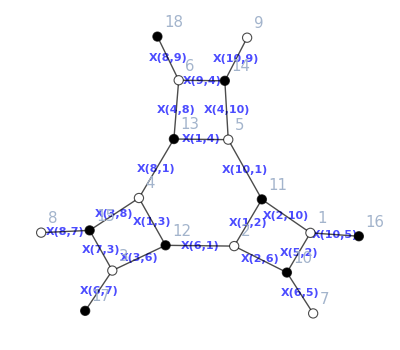

```mathematica
(*SPECIFY WHICH EXAMPLE IT IS*)
ii=10;

(*Below this you don't need to touch*)
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;
topleft=a;
topright=b;
bottomleft=c;
bottomright=d;
viewGraph[a,b,c,d]
```

```mathematica
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
For[ii=1,ii≤76,ii++,
If[ii≠33&&ii≠39&&ii≠50&&ii≠51,
Print["ii=",ii];
(*If[Mod[ii,10]==0,Print["ii=",ii];
];*)
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;

If[Variables[Join[b,c]]=!={},

If[Length[reducibilityBFTedges[a,b,c,d]]≤14,
fullreduction=reductionGraphBFT[a,b,c,d,2];
If[fullreduction=!={},
{newa,newb,newc,newd}={a,b,c,d}/.Map[#->0&,Last[reductionGraphBFT[a,b,c,d,2]]];
,{newa,newb,newc,newd}={a,b,c,d};
];

If[polytopeDim[getPmatrix[newa,newb,newc,newd]]=!=dimensionGrassmannian[newa,newb,newc,newd],
Print["ii=",ii," : There's a problem with dimensionGrassmannian! When a graph is reduced by looking at the moduli space, the master space should have the same dimension as the Grassmannian!"];
];
];

Cmat=getGrassmannian[a,b,c,d];
entries=DeleteCases[Flatten[Cmat],0|1];
combos=Map[Simplify[Times@@#]&,Subsets[entries]];
If[Length[combos]-Length[DeleteDuplicates[combos]]===0,
(*we are not on a secret pole*)
If[Length[entries]=!=dimensionGrassmannian[a,b,c,d],
Print["The dimension of the Grassmannian should be equal to the number of non-trivial entries, when we are not on secret poles!"];
];
,(*we have secret relations among the pluckers*)
If[Length[entries]≤dimensionGrassmannian[a,b,c,d],
Print["ii=",ii," : There's a problem with dimensionGrassmannian! The dimension of the Grassmannian should be less than the number of non-trivial entries, when we are on secret poles!"];
];
];

edges=Variables[joinupKasteleyn[a,b,c,d]];
redgauging1=reducibilityQ[a,b,c,d,False,True,1];
redgauging2=reducibilityQ[a,b,c,d,False,True,2];

pmatrix=getPmatrix[a,b,c,d];
moduligauging1=moduliSpaceBFT[a,b,c,d,1];
If[redgauging1,
If[MemberQ[And@@Map[Length[intoPolytope[moduligauging1[[All,Flatten[Position[#,0]]]]][[2]]]===Length[intoPolytope[moduligauging1][[2]]]&,pmatrix],False],
Print["ii=",ii," : There's a problem with reducibilityQ! The BFT graph is reducible but there are no edges I can remove without removing points in the moduli space!"];
];,
If[FreeQ[And@@Map[Length[intoPolytope[moduligauging1[[All,Flatten[Position[#,0]]]]][[2]]]===Length[intoPolytope[moduligauging1][[2]]]&,pmatrix],False],
Print["ii=",ii," : There's a problem with reducibilityQ! The BFT graph is not reducible but there are edges I can remove without removing points in the moduli space!"];
];
];

If[redgauging2,
If[Cases[edges,zz_/;Length[intoPolytope[moduliSpaceBFT[a/.{zz->0},b/.{zz->0},c/.{zz->0},d,2]][[2]]]===Length[intoPolytope[moduliSpaceBFT[a,b,c,d,2]][[2]]]]==={},
Print["ii=",ii," : There's a problem with reducibilityQ! The BFT graph is reducible but there are no edges I can remove without removing points in the moduli space!"];
];,If[Cases[edges,zz_/;Length[intoPolytope[moduliSpaceBFT[a/.{zz->0},b/.{zz->0},c/.{zz->0},d,2]][[2]]]===Length[intoPolytope[moduliSpaceBFT[a,b,c,d,2]][[2]]]]=!={},
Print["ii=",ii," : There's a problem with reducibilityQ! The BFT graph is not reducible but there are edges I can remove without removing points in the moduli space!"];
];
];

redscattering=reducibilityQ[a,b,c,d,False,False,2];
newentries=Map[Function[{edgeinput},Block[{output},If[Length[Variables[Join[b,c]/.{edgeinput->0}]]≥2,output=DeleteCases[Flatten[getGrassmannian[a/.{edgeinput->0},b/.{edgeinput->0},c/.{edgeinput->0},d]],0|1];,output={};];output]][#]&,edges];

If[redscattering,
If[FreeQ[Map[Length[#]<Length[entries]||Function[{input},Block[{haha,difference},haha=Map[Simplify[Times@@#]&,Subsets[input]];difference=Length[haha]-Length[DeleteDuplicates[haha]];(difference>(Length[combos]-Length[DeleteDuplicates[combos]]))]][#]&,newentries],False],
Print["ii=",ii," : There's a problem with reducibilityQ! The scattering graph is reducible, even though there are no edges which I can remove that keep the same number of elements in the Grassmannian matrix!"];
];
,If[MemberQ[Map[Length[#]<Length[entries]||Function[{input},Block[{haha,difference},haha=Map[Simplify[Times@@#]&,Subsets[input]];difference=Length[haha]-Length[DeleteDuplicates[haha]];(difference>(Length[combos]-Length[DeleteDuplicates[combos]]))]][#]&,newentries],False],
Print["ii=",ii," : There's a problem with reducibilityQ! The scattering graph is not reducible, even though there are edges which I can remove that keep the same number of elements in the Grassmannian matrix!"];
];
];

,Print["We have a dimer"];
];
];
];
```

ii=1

ii=2

ii=3

ii=4

ii=5

ii=6

ii=7

ii=8

ii=9

ii=10

$Aborted

```mathematica
(*Here we are comparing connectivityMatrix with alternativeConnectivityMat*)
```

```mathematica
alternativeConnectivityMat[a_,b_,c_,d_,referencematching_:Null]:=Module[{theperf,adjacencymat,kasteleyn,perfpositions,jj,graph,cyclenodes,turnIntoContributionNothingAdded,cycles,loopnodes,extraloopnodes,toadd,loopcontributions,turnIntoContribution,connectivitymat},
If[referencematching===Null,
theperf=perfectMatchings[a,b,c,d][[lowNumberLoopsPM[a,b,c,d]]];
,theperf=referencematching;
];
adjacencymat=UpperTriangularize[getAdjacencyMatrix[a,b,c,d]];
kasteleyn=joinupKasteleyn[a,b,c,d];
perfpositions=Map[#[[{2,1}]]+{Length[kasteleyn],0}&,Position[kasteleyn,Alternatives@@Variables[theperf]]];
For[jj=1,jj≤Length[perfpositions],jj++,
adjacencymat[[Sequence@@perfpositions[[jj]]]]=1;
adjacencymat[[Sequence@@Reverse[perfpositions[[jj]]]]]=adjacencymat[[Sequence@@Reverse[perfpositions[[jj]]]]]-1;
];

graph=AdjacencyGraph[adjacencymat];

turnIntoContributionNothingAdded=Function[{pathnodes},
Module[{bigmatrix,edges,edgedirections,giveContribution,totalcontrib},
bigmatrix=Join[Join[Table[0,{iii,Length[kasteleyn]},{jjj,Length[kasteleyn]}],Transpose[kasteleyn]],Join[kasteleyn,Table[0,{iii,Dimensions[kasteleyn][[2]]},{jjj,Dimensions[kasteleyn][[2]]}]],2];
edges=Map[bigmatrix[[Sequence@@#]]&,Table[pathnodes[[{iii,iii+1}]],{iii,Length[pathnodes]-1}]];
edgedirections=Map[Ordering[#][[1]]&,Table[pathnodes[[{iii,iii+1}]],{iii,Length[pathnodes]-1}]]/.{2->-1};
giveContribution=Function[{edges,sign},
Block[{contribution},
If[sign==1,
contribution=Total[Intersection[Variables[edges],Complement[Variables[kasteleyn],Variables[theperf]]]];
,contribution=Total[Map[1/#&,Intersection[Variables[edges],Variables[theperf]]]];
];
contribution]
];
totalcontrib=Times@@MapThread[giveContribution[#1,#2]&,{edges,edgedirections}];
totalcontrib
]
];

cycles=FindCycle[graph,Infinity,All]/.{DirectedEdge->List};
loopnodes=Map[#[[Append[Range[1,Length[#],2],Length[#]]]]&,Map[Join@@#&,cycles]];
extraloopnodes={};
For[jj=2,jj≤Length[loopnodes],jj++,
toadd=Cases[Subsets[loopnodes,{jj}],zz_/;Join@@Map[Intersection@@#&,Subsets[zz,{2}]]==={}];
If[toadd==={},
Break[];
];
extraloopnodes=Join[extraloopnodes,toadd];
];
loopnodes=Join[Transpose[{loopnodes}],extraloopnodes];
loopcontributions=Map[Power[-1,Length[#]-1](Times@@#)&,Map[turnIntoContributionNothingAdded,loopnodes,{2}]];
cyclenodes=Map[Union@@#&,loopnodes];

turnIntoContribution=Function[{pathnodes},
Module[{totalcontrib},
totalcontrib=turnIntoContributionNothingAdded[pathnodes];
totalcontrib=totalcontrib/(1-Total[loopcontributions]);
totalcontrib=totalcontrib(1-Total[loopcontributions[[Flatten[Position[Map[Length[Intersection[#,pathnodes]]>0&,cyclenodes],False]]]]]);
totalcontrib
]
];

connectivitymat=Table[FindPath[graph,iii,jjj,Infinity,All],{iii,Total[Dimensions[kasteleyn]]},{jjj,Total[Dimensions[kasteleyn]]}];
connectivitymat=MapThread[Join,{connectivitymat,(DiagonalMatrix[Range[Total[Dimensions[kasteleyn]]]]/.{0->{}})/.{zz_Integer->{{zz}}}},2];
connectivitymat=Map[Total,Map[turnIntoContribution[#]&,connectivitymat,{3}],{2}];
connectivitymat
];
```

```mathematica
alternativetimings={};
normaltimings={};
(*alternativetimings=<<alternativetimings;
normaltimings=<<normaltimings;*)
```

```mathematica
For[ii=1,ii≤76,ii++,
If[ii≠33&&ii≠39&&ii≠50&&ii≠51,
Print["ii=",ii];
(*Below this you don't need to touch*)
formatrule={Subscript[XX_, z1_,z2_]->XX[z1,z2]};
Subscript[bft, ii];
a=a/.formatrule;
b=b/.formatrule;
c=c/.formatrule;
d=d/.formatrule;

perfs=perfectMatchings[a,b,c,d];
srcs=Map[findSources[b,c,#]&,perfs];
multiplic=Map[Tally[srcs][[#,2]]&,Map[Position[Tally[srcs],{#,_}][[1,1]]&,srcs]];

alternative=AbsoluteTiming[alternativeConnectivityMat[a,b,c,d,Null]];
alternativetimings=Append[alternativetimings,{Length[alternative[[2]]],multiplic[[lowNumberLoopsPM[a,b,c,d]]],alternative[[1]]}];
normal=AbsoluteTiming[connectivityMatrix[a,b,c,d,Null]];
normaltimings=Append[normaltimings,{Length[normal[[2]]],multiplic[[lowNumberLoopsPM[a,b,c,d]]],normal[[1]]}];
equals={};
For[jj=1,jj≤Length[perfs],jj++,
If[Mod[jj,10]==0,Print["    jj=",jj];
];
If[multiplic[[jj]]≤3&&jj≠lowNumberLoopsPM[a,b,c,d],
alternative=AbsoluteTiming[alternativeConnectivityMat[a,b,c,d,perfs[[jj]]]];
alternativetimings=Append[alternativetimings,{Length[alternative[[2]]],multiplic[[jj]],alternative[[1]]}];
normal=AbsoluteTiming[connectivityMatrix[a,b,c,d,perfs[[jj]]]];
normaltimings=Append[normaltimings,{Length[normal[[2]]],multiplic[[jj]],normal[[1]]}];
equals=Append[equals,Simplify[alternative[[2]]==normal[[2]]]===True];
];
];
If[And@@equals=!=True,
Print["There is a PROBLEM!!!"];
];
];
];
```

ii=1

ii=2

ii=3

jj=10

ii=4

ii=5

ii=6

jj=10

ii=7

ii=8

ii=9

jj=10

jj=20

ii=10

jj=10

jj=20

jj=30

jj=40

jj=50

ii=11

jj=10

jj=20

ii=12

jj=10

jj=20

jj=30

jj=40

ii=13

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

jj=90

jj=100

jj=110

ii=14

jj=10

jj=20

jj=30

jj=40

ii=15

jj=10

jj=20

jj=30

jj=40

ii=16

ii=17

ii=18

ii=19

ii=20

jj=10

ii=21

ii=22

jj=10

ii=23

jj=10

ii=24

jj=10

ii=25

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=26

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

jj=90

jj=100

jj=110

jj=120

jj=130

jj=140

jj=150

jj=160

jj=170

jj=180

jj=190

jj=200

jj=210

jj=220

jj=230

jj=240

jj=250

jj=260

jj=270

jj=280

jj=290

jj=300

jj=310

jj=320

jj=330

jj=340

ii=27

jj=10

jj=20

jj=30

ii=28

jj=10

jj=20

jj=30

jj=40

ii=29

jj=10

jj=20

jj=30

jj=40

ii=30

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

ii=31

jj=10

jj=20

jj=30

ii=32

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

ii=34

ii=35

ii=36

jj=10

ii=37

jj=10

jj=20

jj=30

ii=38

jj=10

jj=20

jj=30

jj=40

ii=40

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=41

jj=10

jj=20

jj=30

ii=42

jj=10

jj=20

jj=30

ii=43

jj=10

jj=20

jj=30

jj=40

ii=44

jj=10

jj=20

jj=30

jj=40

ii=45

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=46

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=47

jj=10

jj=20

jj=30

jj=40

jj=50

ii=48

jj=10

ii=49

jj=10

ii=52

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

ii=53

jj=10

jj=20

jj=30

jj=40

ii=54

ii=55

ii=56

ii=57

jj=10

jj=20

ii=58

jj=10

jj=20

ii=59

jj=10

jj=20

jj=30

jj=40

ii=60

jj=10

jj=20

jj=30

jj=40

ii=61

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

jj=70

jj=80

jj=90

jj=100

jj=110

jj=120

jj=130

jj=140

jj=150

jj=160

jj=170

jj=180

jj=190

jj=200

ii=62

jj=10

jj=20

jj=30

jj=40

ii=63

jj=10

jj=20

jj=30

ii=64

jj=10

jj=20

jj=30

ii=65

ii=66

jj=10

ii=67

jj=10

jj=20

ii=68

jj=10

jj=20

jj=30

jj=40

ii=69

jj=10

jj=20

jj=30

jj=40

ii=70

jj=10

ii=71

ii=72

jj=10

ii=73

jj=10

ii=74

jj=10

jj=20

jj=30

jj=40

jj=50

jj=60

ii=75

jj=10

jj=20

jj=30

jj=40

ii=76

jj=10

jj=20

jj=30

jj=40

```mathematica
normaltimings>>normaltimings;
alternativetimings>>alternativetimings;
```

{cc→3.09221}

{cc→2.8752}

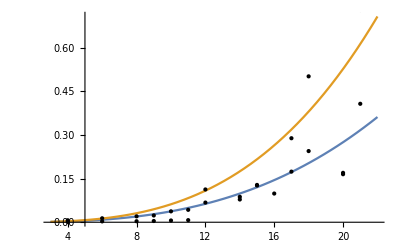

```mathematica
multiplicity=1;
datanormal=Sort[Map[Mean,GatherBy[Map[#[[{1,3}]]&,Cases[normaltimings,{_,multiplicity,_}]],First]]];
dataalternative=Sort[Map[Mean,GatherBy[Map[#[[{1,3}]]&,Cases[alternativetimings,{_,multiplicity,_}]],First]]];
(*ListPlot[{dataalternative,datanormal},PlotRange->All]*)

normalmodel=0.00005(1+(multiplicity-1)0.1465048478811045) xx^cc;
normalfit=Chop[FindFit[datanormal,normalmodel,{cc},xx],10^-6]
normalline=Function[{xx},Evaluate[normalmodel/.normalfit]];

alternativemodel=0.00005(1+(multiplicity-1)0.007644753105478895) xx^cc;
alternativefit=Chop[FindFit[dataalternative,alternativemodel,{cc},xx],10^-6]
alternativeline=Function[{xx},Evaluate[alternativemodel/.alternativefit]];

(*normalmodel=bb xx^cc;
normalfit=Chop[FindFit[datanormal,normalmodel,{bb,cc},xx],10^-6]
alternativemodel=bb xx^cc;
alternativefit=Chop[FindFit[dataalternative,alternativemodel,{bb,cc},xx],10^-6]
Mean[{bb/.normalfit,bb/.alternativefit}]
generalmodel=Mean[{bb/.normalfit,bb/.alternativefit}] xx^cc;
normalfit=Chop[FindFit[datanormal,generalmodel,{cc},xx],10^-6]
alternativefit=Chop[FindFit[dataalternative,generalmodel,{cc},xx],10^-6]
normalline=Function[{xx},Evaluate[generalmodel/.normalfit]];
alternativeline=Function[{xx},Evaluate[generalmodel/.alternativefit]];*)

Plot[{alternativeline[xx],normalline[xx]},{xx,3,22},Epilog->Join[Map[Point[#,VertexColors->Blue]&,dataalternative],Map[Point[#,VertexColors->Orange]&,datanormal]],PlotRange->All]
```

```mathematica
(3.066405674612687+3.3439258526263114+3.655882974069246+3.6219425472110225)/4
(2.843363175648133+2.883866314082025+3.0093816895347447+2.960523322034808)/4
```

3.42204

2.92428

0.146505

0.00764475

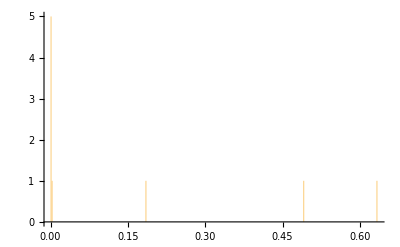

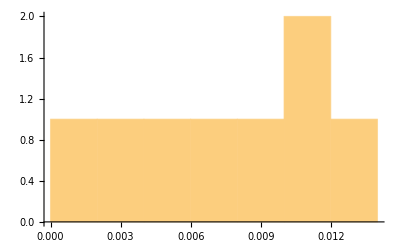

```mathematica
normalgradient={};
alternativegradient={};
For[size=1,size≤24,size++,
datanormal=Sort[Map[Mean,GatherBy[Map[#[[{2,3}]]&,Cases[normaltimings,{size,_,_}]],First]]];
dataalternative=Sort[Map[Mean,GatherBy[Map[#[[{2,3}]]&,Cases[alternativetimings,{size,_,_}]],First]]];
(*ListPlot[{dataalternative,datanormal},PlotRange->All]*)

If[Length[datanormal]≥2,

normalmodel=aa+bb xx;
normalfit=FindFit[datanormal,normalmodel,{aa,bb},xx];
normalgradient=Append[normalgradient,bb/.normalfit];
normalline=Function[{xx},Evaluate[normalmodel/.normalfit]];

alternativemodel=aa+bb xx;
alternativefit=FindFit[dataalternative,alternativemodel,{aa,bb},xx];
alternativegradient=Append[alternativegradient,bb/.alternativefit];
alternativeline=Function[{xx},Evaluate[alternativemodel/.alternativefit]];

(*Print[Plot[{alternativeline[xx],normalline[xx]},{xx,0.5,Max[Transpose[datanormal][[1]]]+0.5},Epilog->Join[Map[Point[#,VertexColors->Blue]&,dataalternative],Map[Point[#,VertexColors->Orange]&,datanormal]],PlotRange->All]];
Print[Last[normalgradient]];*)
];
];
Mean[DeleteCases[normalgradient,zz_/;zz>2Median[normalgradient]]]
Mean[DeleteCases[alternativegradient,zz_/;zz>2Median[alternativegradient]]]
Histogram[DeleteCases[normalgradient,zz_/;zz>2Median[normalgradient]],200]
Histogram[DeleteCases[alternativegradient,zz_/;zz>2Median[alternativegradient]],6]
```

```mathematica
(*THIS IS THE TIME IT TAKES FOR A COMPUTATION!*)
finalmodelNORMAL[size_,multiplicity_]:=0.00005(1+(multiplicity-1)0.1465048478811045) size^3.422039262129817;
(*finalmodelNORMAL[size_,multiplicity_]:=0.00005(1+(multiplicity-1)0.4965048478811045) size^3.402039262129817;*)
finalmodelALTERNATIVE[size_,multiplicity_]:=0.00005(1+(multiplicity-1)0.007644753105478895) size^2.924283625324928;

Mean[Map[finalmodelNORMAL[#[[1]],#[[2]]]-#[[3]]&,normaltimings]]
Mean[Map[Abs[finalmodelNORMAL[#[[1]],#[[2]]]-#[[3]]]&,normaltimings]]
Mean[Map[finalmodelALTERNATIVE[#[[1]],#[[2]]]-#[[3]]&,alternativetimings]]
Mean[Map[Abs[finalmodelALTERNATIVE[#[[1]],#[[2]]]-#[[3]]]&,alternativetimings]]
```

-3.04997

3.58308

-0.188793

0.188793

```mathematica
FindMinimum[Mean[Map[Abs[(0.0000023(1+(#[[2]]-1)multcoeff) (#[[1]])^exponent)-#[[3]]]&,normaltimings]],{{multcoeff,0.1465048478811045},{exponent,3.422039262129817}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.25033,{multcoeff→120.203,exponent→2.91427}}

```mathematica
FindMinimum[Mean[Map[Abs[(0.000023(1+(#[[2]]-1)multcoeff) (#[[1]])^exponent)-#[[3]]]&,alternativetimings]],{{multcoeff,0.007644753105478895},{exponent,2.924283625324928}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0571947,{multcoeff→0.356511,exponent→3.07294}}

```mathematica
loadupnormal=<<normaltimings;
loadupalternative=<<alternativetimings;
```

```mathematica
FindMinimum[Mean[Map[Abs[(0.0000023(1+(#[[2]]-1)multcoeff) (#[[1]])^exponent)-#[[3]]]&,loadupnormal]],{{multcoeff,0.1465048478811045},{exponent,3.422039262129817}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.06266,{multcoeff→194.422,exponent→2.71977}}

```mathematica
FindMinimum[Mean[Map[Abs[(0.000023(1+(#[[2]]-1)multcoeff) (#[[1]])^exponent)-#[[3]]]&,loadupalternative]],{{multcoeff,0.007644753105478895},{exponent,2.924283625324928}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0561878,{multcoeff→0.359089,exponent→3.0413}}

```mathematica
FindMinimum[Mean[Map[Abs[(0.0000023(1+(#[[2]]-1)multcoeff) (#[[1]])^exponent)-#[[3]]]&,Join[normaltimings,loadupnormal]]],{{multcoeff,0.1465048478811045},{exponent,3.422039262129817}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{3.15735,{multcoeff→124.908,exponent→2.88826}}

```mathematica
FindMinimum[Mean[Map[Abs[(0.000023(1+(#[[2]]-1)multcoeff) (#[[1]])^exponent)-#[[3]]]&,Join[alternativetimings,loadupalternative]]],{{multcoeff,0.007644753105478895},{exponent,2.924283625324928}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0570451,{multcoeff→0.351048,exponent→3.06163}}

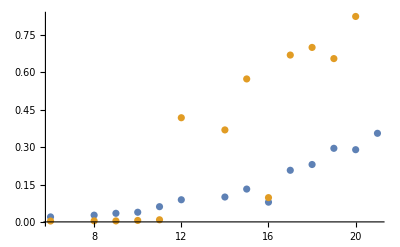

```mathematica
getmean[list_]:=Map[Mean,GatherBy[DeleteCases[Map[#[[{1,3}]]&,Cases[list,{_,2,_}]],zz_/;Last[zz]>1],First]];
ListPlot[{getmean[alternativetimings],getmean[normaltimings]},PlotRange->All]
```